## Calculate in the Infinite Stripe Geometry i.e., no hopping between the 1st and Nth sites (with the corrected Hamiltonian).

```mathematica
dimensionN=20
```

20

Note: I have tried and realized that analytical solution when N=20 is impractical. (I aborted the program after 1 hour of running without result.)

Now Construct the Hamiltonian Matrix

```mathematica
A=ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2;
A//MatrixForm
```

(-1/2 | 1/2
-1/2 | 1/2)

```mathematica
B[px_,m_]:=2Sin[px]*PauliMatrix[1]/2-2Cos[px]PauliMatrix[3]/2+(2-m)PauliMatrix[3];
B[px,m]//MatrixForm
```

(2-m-Cos[px] | Sin[px]
Sin[px] | -2+m+Cos[px])

```mathematica
CMatrix=-ⅈ*PauliMatrix[2]/2-PauliMatrix[3]/2;
CMatrix//MatrixForm
```

(-1/2 | -1/2
1/2 | 1/2)

```mathematica
For[i=1,i≤ dimensionN,i++,
If[i==1,
hamiltonianMLine[i][px_,m_]=ArrayFlatten[{{B[px,m],CMatrix,ConstantArray[0,{2,2*dimensionN-4}]}}]
];
If[i>1&&i<dimensionN,
hamiltonianMLine[i][px_,m_]=ArrayFlatten[{{
ConstantArray[0,{2,2*(i-2)}],A,B[px,m],CMatrix,ConstantArray[0,{2,2*dimensionN-2*(i+1)}]
}}]
];
If[i==dimensionN,
hamiltonianMLine[i][px_,m_]=ArrayFlatten[{{
ConstantArray[0,{2,2*(i-2)}],A,B[px,m]
}}]
];]
hamiltonianM[px_,m_]=hamiltonianMLine[1][px,m];
For[i=2,i≤dimensionN,i++,
hamiltonianM[px_,m_]=Join[hamiltonianM[px,m],hamiltonianMLine[i][px,m]];
];
hamiltonianM[px,m]//MatrixForm
```

(2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px] | -1/2 | -1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px] | 1/2 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | 2-m-Cos[px] | Sin[px]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2 | Sin[px] | -2+m+Cos[px])

Solve the Eigenvalue Equation and Plot

```mathematica
eigenSystemResult[px_,m_]:=Eigensystem[hamiltonianM[px,m]]
(* Use delayed assignment := instead of = so that we could make a numerical analysis later *)
```

The eigensystem returns a 2 x (2*dimensionN) matrix, with the eigenvalues in the first line, and the corresponding eigenvectors in the second line. 
Now I plot their eigenvalues. But before actually plotting, I tried to see which combination of PlotPoints and MaxRecursion gives a good result. See Documentation: howto/MakeASmootherOrRougherPlot for PlotPoints v.s. MaxRecursion

```mathematica
ListPlot3D[
Table[
First[
Timing[Plot[eigenSystemResult[px,1][[1,1]],{px,-π,π},MeshStyle->{PointSize[Tiny],Blue},Mesh->All,PlotStyle->None,PlotPoints->plt,MaxRecursion->rec]]
],
{plt,6,12},{rec,1,4}]]
```

-Graphics3D-

After several trial, I found the following combination to be satisfactory.

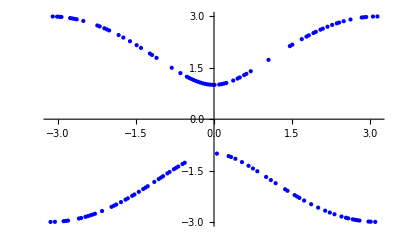

```mathematica
Plot[eigenSystemResult[px,1][[1,1]],{px,-π,π},MeshStyle->{PointSize[Tiny],Blue},Mesh->All,PlotStyle->None,PlotPoints->10,MaxRecursion->4]
```

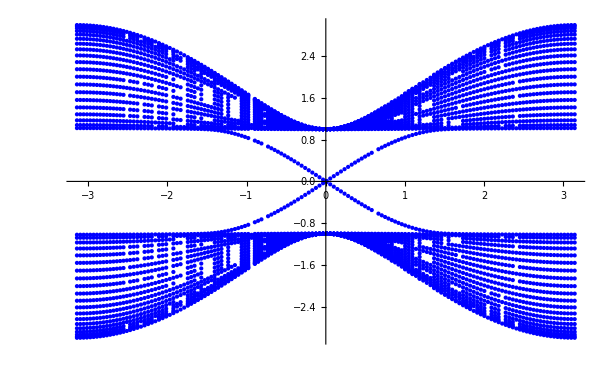

```mathematica
Plot[Table[eigenSystemResult[px,1][[1,i]],{i,2*dimensionN}],{px,-π,π},MeshStyle->{PointSize[Tiny],Blue},Mesh->All,PlotStyle->None,PlotPoints->10,MaxRecursion->4]
```

Let me try to manipulate the mass m, using a cost effective (PlotPoints, MaxRecursion)=(6,4):

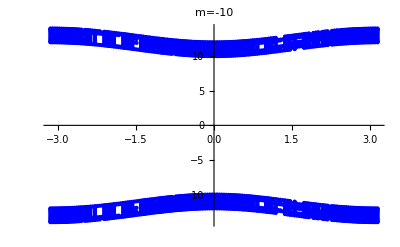
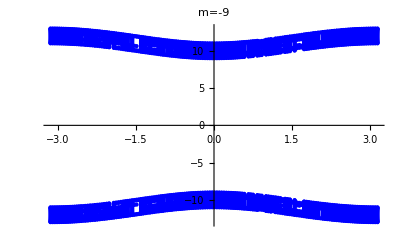
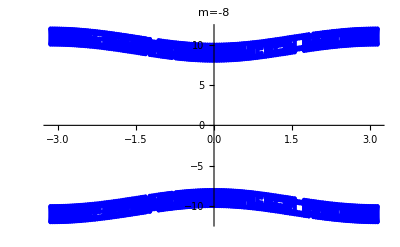
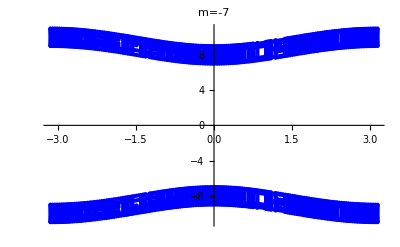
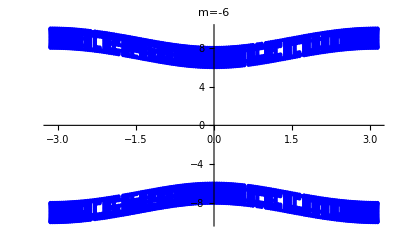
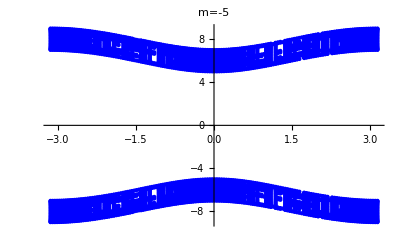
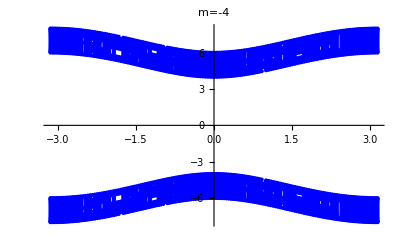
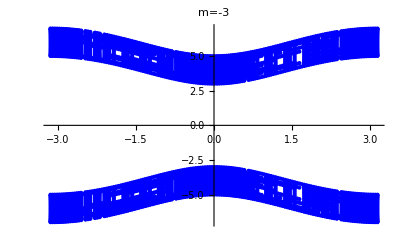

```mathematica
tableOfSpecturmVSm=Table[
Plot[Table[eigenSystemResult[px,m][[1,i]],{i,2*dimensionN}],{px,-π,π},MeshStyle->{PointSize[Tiny],Blue},Mesh->All,PlotStyle->None,PlotPoints->10,MaxRecursion->4,PlotLabel->"m="<>ToString[m]],
{m,-10,10}]
```

To confirm the crossing, plot the data at specific values of m with more precision:
For m=-1 to 4

To find out more about them, I calculate the eigenvalues in the libraray’s PC (which runs faster than my notebook), and copy the results below.

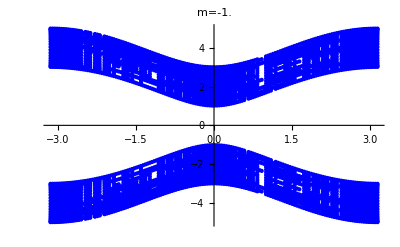
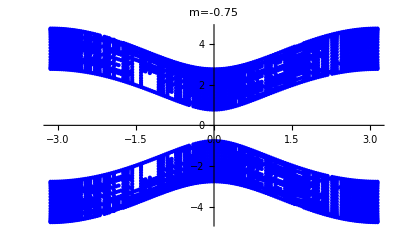
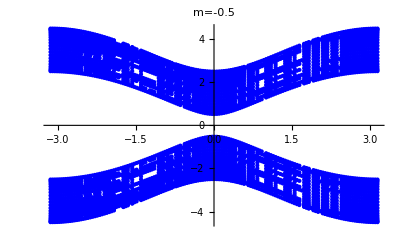
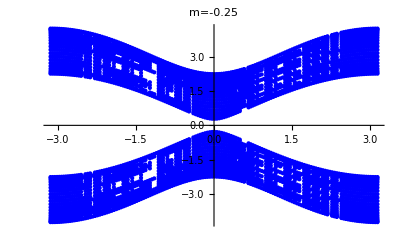
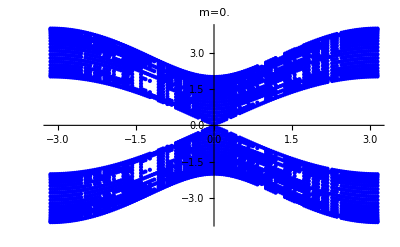
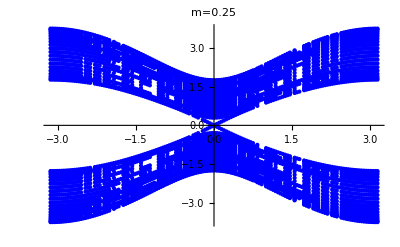
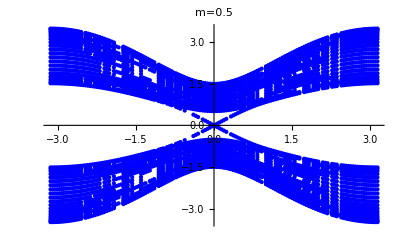
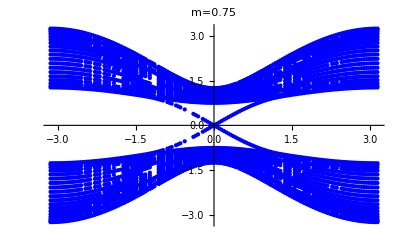

```mathematica
tableOfSpecturmVSm=ParallelTable[
Plot[Table[eigenSystemResult[px,m][[1,i]],{i,2*dimensionN}],{px,-π,π},MeshStyle->{PointSize[Tiny],Blue},Mesh->All,PlotStyle->None,PlotPoints->10,MaxRecursion->4,PlotLabel->"m="<>ToString[m]],
(*{m,-1,4}]*)
{m,-1,4.6,0.25}]
```